# RB-SFA: High Harmonic Generation in the Strong Field Approximation via Mathematica

© Emilio Pisanty 2014-2015. Licensed under GPL and CC-BY-SA.

## Introduction

### Readme

RB-SFA is a compact and flexible Mathematica package for calculating High Harmonic Generation emission within the Strong Field Approximation. It combines Mathematica’s analytical integration capabilities with its numerical calculation capacities to offer a fast and user-friendly plug-and-play solver for calculating harmonic spectra and other properties. In addition, it can calculate first-order nondipole corrections to the SFA results to evaluate the effect of the driving laser’s magnetic field on harmonic spectra.

The name RB-SFA comes from its first application (as Rotating Bicircular High Harmonic Generation in the Strong field Approximation) but the code is general so RB-SFA just stands for itself now. This first application was used to calculate the polarization properties of the harmonics produced by multi-colour circularly polarized fields, as reported in the paper

    Spin conservation in high-order-harmonic generation using bicircular fields. E. Pisanty, S. Sukiasyan and M. Ivanov. Phys. Rev. A 90, 043829 (2014), arXiv:1404.6242.

This code is dual-licensed under the GPL and CC-BY-SA licenses. If you use this code or its results in an academic publication, please cite the paper above or the GitHub repository where the latest version will always be available. An example citation is 

    E. Pisanty. RB-SFA: High Harmonic Generation in the Strong Field Approximation via Mathematica. https://github.com/episanty/RB-SFA (2014).

This software consists of this notebook, which contains the code and its documentation, a corresponding auto-generated package file. This notebook also contains a Usage and Examples section which explains how to use the code and documents the calculations used in the original publication.

### Specifications

This code calculates the harmonic dipole as per the original Lewenstein et al. paper,

    M. Lewenstein, Ph. Balcou, M.Yu. Ivanov, A. L’Huillier and P.B. Corkum. Theory of high-harmonic generation by low-frequency laser fields. Phys. Rev. A 49 no. 3, 2117 (1994).
    
The time-dependent dipole is given by

          D(t)=ⅈ∫_0^t ⅆt'∫ⅆ^3 p d(π(p,t)) × F(t')·d(π(p,t))×exp[-ⅈ S(p,t,t')]+c.c.

Here F(t)is the time-dependent applied electric field, with vector potential A(t); the electron charge is taken to be -1. The integration time t' can be interpreted as the ionization time and the integration limit t represents the recollision time. (Upon applying the saddle-point approximation to the temporal integrals these notions apply exactly to the corresponding quantum orbits.) The ionization and recollision events are governed by the corresponding dipole matrix elements, which are taken for a hydrogenic 1s-type orbital with characteristic momentum κ and ionization potential I_p=1/2 κ^2:

    d(p)=p d̂ g=(8ⅈ)/π(√(2 κ^5)p)/((p^2+κ^2)^3).

(Taken from B. Podolsky & L. Pauling. Phys. Rev. 34 no. 1, 109 (1929).) The displaced momentum π(p,t)=p+A(t) is used to aid in the generalization to nondipole cases.

The action 

    S(p,t,t')=∫_t'^t (1/2 κ^2+1/2(π(p,τ))^2)ⅆτ 

is the governing factor of the integral. It is highly oscillatory and must be dealt with carefully. The momentum integral is approximated using the saddle point method; this is valid and straightforward since there is always one unique saddle point,

    p(t,t')=-(∫_t'^t A(t'')ⅆt'')/(t-t'),
    
as long as the action’s dependence on the momentum is quadratic. After the momentum has been integrated via the saddle point method, the time-dependent dipole is given by

          D(t)=ⅈ∫_0^t ⅆt'((2π)/(ϵ+ⅈ(t-t')))^(3/2) d(π(p_s(t,t'),t)) × F(t')·d(π(p_s(t,t'),t))×exp[-ⅈ S(p(t,t'),t,t')]+c.c.
          
A regularization factor ϵ has been introduced to prevent divergence of the prefactor as t' approaches t, representing the fact that at t=t' the p integral no longer has a quadratic exponent.

The integral is performed with respect to the excursion time τ=t-t' for simplicity. To reduce integration time, a gating function gate[ω τ] has been introduced, and the integration time has been cut short to a controllable length. This is physically reasonable as the wavepacket spreading (which scales as τ^(-3/2)) makes the contributions after the gate negligible.
More physically, supressing the contributions from large excursion times represents the fact that the extra-long trajectories they represent produce harmonics which are much harder to phase match (as their harmonic phase is very sensitively dependent on many factors) which means that they are rarely present in experimental spectra unless a concerted effort is performed to observe them.

### First-order nondipole calculations

This code can also be used to calculate the first-order effect of nondipole terms, which become relevant at high intensities or long wavelengths, when the electron’s speed from the laser-driven oscillations (which scales as F/ω) becomes comparable to the speed of light (equal to c=1/α≈137 in atomic units). (More specifically, the nondipole effects on the harmonic generation become relevant when the magnetic pushing per cycle, which offsets the returning wavepacket by F^2/cω^3, becomes comparable with the wavepacket spread upon recollision.)

This code implements a generalization of the theory presented in various forms in the papers N.J. Kylstra et al. J. Phys B: At. Mol. Opt. Phys. 34 no. 3, L55 (2001); N..J. Kylstra et al. Laser Phys. 12 no. 2, 409 (2002); M.W. Walser et al. Phys. Rev. Lett. 85 no. 24, 5082 (2000); V. Averbukh et al. Phys Rev. A 65, 063402 (2002); and C.C. Chirilă et al. Phys. Rev. A 66, 063411 (2002).

The nondipole-HHG code calculates the harmonic dipole of exactly the same form as the standard SFA,

          D(t)=ⅈ∫_0^t ⅆt'∫ⅆ^3 p d(π(p,t)) × F(t')·d(π(p,t))×exp[-ⅈ S(p,t,t')]+c.c.

with S(p,t,t')=∫_t'^t ⅆt''(1/2 κ^2+1/2(π(p,t''))^2)  as before, but with a nondipole term in the displaced momentum, which now reads

          π(p,t))=p+A(t)-∫^t ∇A(τ)·(p+A(τ))ⅆτ,
          
or in component notation

          π_j(p,t))=p_j+A_j(t)-∫^t ∂_j A_k(τ)(p_k+A_k(τ))ⅆτ.

## Implementation: supporting functions

### Initialization

```mathematica
BeginPackage["RBSFA`"];
```

### The dipole transition matrix element

```mathematica
dipole::usage="dipole[p,κ] returns the dipole transition matrix element for a 1s hydrogenic state of ionization potential I_p=1/2κ^2.";
Begin["`Private`"];
dipole[p_,κ_]:=(8ⅈ)/π(√(2 κ^5)p)/((Norm[p]^2+κ^2)^3)
End[];
```

### Various field envelopes

#### flatTopEnvelope

```mathematica
flatTopEnvelope::usage="flatTopEnvelope[ω,num,nRamp] returns a Function object representing a flat-top envelope at carrier frequency ω lasting a total of num cycles and with linear ramps nRamp cycles long.";
Begin["`Private`"];
flatTopEnvelope[ω_,num_,nRamp_]:=Function[t,Piecewise[{{0,t<0},{Sin[(ω t)/(4nRamp)]^2,0≤t<(2 π)/ω nRamp},{1,(2 π)/ω nRamp≤t<(2 π)/ω(num-nRamp)},{Sin[(ω ((2 π)/ω num-t))/(4nRamp)]^2,(2 π)/ω(num-nRamp)≤t<(2 π)/ω num},{0,(2 π)/ω num≤t}}]]
End[];
```

#### cosPowerFlatTop

```mathematica
cosPowerFlatTop::usage="cosPowerFlatTop[ω,num,power] returns a Function object representing a smooth flat-top envelope of the form 1-Cos(ω t/2 num)^power";
Begin["`Private`"];
cosPowerFlatTop[ω_,num_,power_]:=Function[t,1-Cos[(ω t)/(2num)]^power]
End[];
```

### Field duration standard options

The standard options for the duration of the pulse and the resolution are

```mathematica
PointsPerCycle::usage="PointsPerCycle is a sampling option which specifies the number of sampling points per cycle to be used in integrations.";
TotalCycles::usage="TotalCycles is a sampling option which specifies the total number of periods to be integrated over.";
CarrierFrequency::usage="CarrierFrequency is a sampling option which specifies the carrier frequency to be used.";
Protect[PointsPerCycle,TotalCycles,CarrierFrequency];
```

```mathematica
standardOptions={PointsPerCycle->90,TotalCycles->1,CarrierFrequency->0.057};
```

PointsPerCycle dictates how many sampling points are used per laser cycle (at frequency CarrierFrequency, of the infrared laser), and it should be at least twice the highest harmonic of interest. The total duration is TotalCycles cycles. CarrierFrequency is the frequency of the fundamental laser, in atomic units.

### harmonicOrderAxis

harmonicOrderAxis produces a list that can be used as a harmonic order axis for the given pulse parameters. 

The length can be fine-tuned (to match exactly a spectrum, for instance, and get a matrix of the correct shape) using the correction option, or a TargetLength can be directly specified.

```mathematica
harmonicOrderAxis::usage="harmonicOrderAxis[opt→value] returns a list of frequencies which can be used as a frequency axis for Fourier transforms, scaled in units of harmonic order, for the provided field duration and sampling options.";
TargetLength::usage="TargetLength is an option for harmonicOrderAxis which specifies the total length required of the resulting list.";
LengthCorrection::usage="LengthCorrection is an option for harmonicOrderAxis which allows for manual correction of the length of the resulting list.";
Protect[LengthCorrection,TargetLength];
Begin["`Private`"];
Options[harmonicOrderAxis]=standardOptions~Join~{TargetLength->Automatic,LengthCorrection->1};
harmonicOrderAxis::target="Invalid TargetLength option `1`. This must be a positive integer or Automatic.";
harmonicOrderAxis[OptionsPattern[]]:=Module[{num=OptionValue[TotalCycles],npp=OptionValue[PointsPerCycle]},
Piecewise[{
{1/num Range[0.,Round[(npp num+1)/2.]-1+OptionValue[LengthCorrection]],OptionValue[TargetLength]===Automatic},
{Round[(npp num+1)/2.]/num Range[0,OptionValue[TargetLength]-1]/OptionValue[TargetLength],IntegerQ[OptionValue[TargetLength]]&&OptionValue[TargetLength]≥0}
},
Message[harmonicOrderAxis::target,OptionValue["TargetLength"]];Abort[]
]
]
End[];
```

### frequencyAxis

frequencyAxis produces a list that can be used as a harmonic order axis for the given pulse parameters. Identical to harmonicOrderAxis but produces a frequency axis (in atomic units) instead.

```mathematica
frequencyAxis::usage="frequencyAxis[opt→value] returns a list of frequencies which can be used as a frequency axis for Fourier transforms, in atomic units of frequency, for the provided field duration and sampling options.";
Begin["`Private`"];
Options[frequencyAxis]=Options[harmonicOrderAxis];
frequencyAxis[options:OptionsPattern[]]:=OptionValue[CarrierFrequency]harmonicOrderAxis[options]
End[];
```

### timeAxis

timeAxis produces a list that can be used as a time axis for the given pulse parameters.

```mathematica
Quit
```

```mathematica
timeAxis::usage="timeAxis[opt→value] returns a list of times which can be used as a time axis ";
TimeScale::usage="TimeScale is an option for timeAxis which specifies the units the list should use: AtomicUnits by default, or LaserPeriods if required.";
AtomicUnits::usage="AtomicUnits is a value for the option TimeScale of timeAxis which specifies that the times should be in atomic units of time.";
LaserPeriods::usage="LaserPeriods is a value for the option TimeScale of timeAxis which specifies that the times should be in multiples of the carrier laser period.";
Protect[TimeScale,AtomicUnits,LaserPeriods];
Begin["`Private`"];
Options[timeAxis]=standardOptions~Join~{TimeScale->AtomicUnits};
timeAxis::scale="Invalid TimeScale option `1`. Available values are AtomicUnits and LaserPeriods";
timeAxis[OptionsPattern[]]:=Block[{T=2π/ω,ω=OptionValue[CarrierFrequency],num=OptionValue[TotalCycles],npp=OptionValue[PointsPerCycle]},
Piecewise[{
{1,OptionValue[TimeScale]==AtomicUnits},
{1/T,OptionValue[TimeScale]==LaserPeriods}
},
Message[timeAxis::scale,OptionValue[TimeScale]];Abort[]
]×Table[t
,{t,0,num(2π)/ω,num/(num×npp+1)(2π)/ω}
]
]
End[];
```

### getSpectrum

getSpectrum takes a time-dependent dipole list and returns its Fourier transform in absolute-value-squared. It takes as options
  · pulse parameters ω, TotalCycles and PointsPerCycle,
  · a polarization parameter ϵ, which gives an unpolarized spectrum when given False, or polarizes along an ellipticity vector ϵ (this is meant primarily to select right- and left-circularly polarized spectra using ϵ={1,ⅈ} and ϵ={1,-ⅈ} respectively),
  · a DifferentiationOrder, which can return the dipole value (default,=0), velocity (=1), or acceleration (=2), 
  · a power of ω, ωPower, with which to multiply the spectrum before returning it (which should be equivalent to DifferentiationOrder except for pathological cases), and
  · a ComplexPart function to apply immediately after differentiation (default is the identity function, but Re, Im, or Abs[#]^2& are reasonable choices).
If no option is passed to ωPower and DifferentiationOrder, the pulse parameters do not really affect the output, except by a global factor of TotalCycles.

```mathematica
getSpectrum::usage="getSpectrum[DipoleList] returns the power spectrum of DipoleList.";
Polarization::usage="Polarization is an option for getSpectrum which specifies a polarization vector along which to polarize the dipole list. The default, Polarization→False, specifies an unpolarized spectrum.";
ComplexPart::usage="part is an option for getSpectrum which specifies a function (like Re, Im, or by default #&) which should be applied to the dipole list before the spectrum is taken.";
ωPower::usage="ωPower is an option for getSpectrum which specifies a power of frequency which should multiply the spectrum.";
DifferentiationOrder::usage="DifferentiationOrder is an option for getSpectrum which specifies the order to which the dipole list should be differentiated before the spectrum is taken.";
Protect[Polarization,part,ωPower,DifferentiationOrder];

Begin["`Private`"];
Options[getSpectrum]={Polarization->False,ComplexPart->(#&),ωPower->0,DifferentiationOrder->0}~Join~standardOptions;

getSpectrum::diffOrd="Invalid differentiation order `1`.";
getSpectrum::ωPow="Invalid ω power `1`.";

getSpectrum[dipoleList_,OptionsPattern[]]:=Block[
{polarizationVector,differentiatedList,depth,dimensions,
num=OptionValue[TotalCycles],npp=OptionValue[PointsPerCycle],ω=OptionValue[CarrierFrequency],δt=(2π/ω)/npp
},
polarizationVector=OptionValue[Polarization]/Norm[OptionValue[Polarization]];

differentiatedList=OptionValue[ComplexPart][Piecewise[{
{dipoleList,OptionValue[DifferentiationOrder]==0},
{1/(2δt)(Most[Most[dipoleList]]-Rest[Rest[dipoleList]]),OptionValue[DifferentiationOrder]==1},
{1/δt^2(Most[Most[dipoleList]]-2Most[Rest[dipoleList]]+Rest[Rest[dipoleList]]),OptionValue[DifferentiationOrder]==2}},
Message[getSpectrum::diffOrd,OptionValue[DifferentiationOrder]];Abort[]
]];

If[NumberQ[OptionValue[ωPower]],Null;,Message[getSpectrum::ωPow,OptionValue[ωPower]];Abort[]  ];

num Table[
(ω/num k)^(2OptionValue[ωPower]),{k,1,Round[Length[differentiatedList]/2]}
]×If[
OptionValue[Polarization]===False,(*unpolarized spectrum*)
(*funky depth thing so this can take lists of numbers and lists of vectors, of arbitrary length. Makes for easier benchmarking.*)
depth=Length[Dimensions[dipoleList]];
dimensions=If[Length[#]>1,#⟦2⟧,1(*#⟦1⟧*)]&[Dimensions[dipoleList]];
Sum[Abs[
Fourier[
If[depth>1,Re[differentiatedList⟦All,i⟧],Re[differentiatedList⟦All⟧]]
,FourierParameters->{-1, 1}
]⟦1;;Round[Length[differentiatedList]/2]⟧
]^2,{i,1,dimensions}]
,(*polarized spectrum*)
Abs[
Transpose[Table[
Fourier[
Re[differentiatedList⟦All,i⟧]
,FourierParameters->{-1, 1}
]
,{i,1,2}]]⟦1;;Round[Length[differentiatedList]/2]⟧.polarizationVector
]^2
]
]
End[];
```

### spectrumPlotter

spectrumPlotter takes a spectrum and a list of options and returns a plot of the spectrum. The available options are
  · a FrequencyAxis option, which will give the harmonic order as a horizontal axis by default, and an arbitrary scale with any other option,
  · all the options of harmonicOrderAxis, which will be passed to the call that makes the horizontal axis, and
  · all the options of ListLinePlot, which will be used to format the plot.

```mathematica
spectrumPlotter::usage="spectrumPlotter[spectrum] plots the given spectrum with an appropriate axis in a log_10 scale.";
FrequencyAxis::usage="FrequencyAxis is an option for spectrumPlotter which specifies the axis to use.";
Protect[FrequencyAxis];
Begin["`Private`"];
Options[spectrumPlotter]=Join[{FrequencyAxis->"HarmonicOrder"},Options[harmonicOrderAxis],Options[ListLinePlot]];
spectrumPlotter[spectrum_,options:OptionsPattern[]]:=ListPlot[
{Which[
OptionValue[FrequencyAxis]==="HarmonicOrder",
harmonicOrderAxis["TargetLength"->Length[spectrum],Sequence@@FilterRules[{options}~Join~Options[spectrumPlotter],Options[harmonicOrderAxis]]],
OptionValue[FrequencyAxis]==="Frequency",
frequencyAxis["TargetLength"->Length[spectrum],Sequence@@FilterRules[{options}~Join~Options[spectrumPlotter],Options[harmonicOrderAxis]]],
True,Range[Length[spectrum]]
],
Log[10,spectrum]
}ᵀ
,Sequence@@FilterRules[{options},Options[ListLinePlot]]
,Joined->True
,PlotRange->Full
,PlotStyle->Thick
,Frame->True
,Axes->False
,ImageSize->800
]
End[];
```

### biColorSpectrum

biColorSpectrum takes a time-dependent dipole list and produces overlaid plots of the right- and left-circular components of the spectrum, in red and blue respectively. It takes all the options of getSpectrum and spectrumPlotter, which are passed directly to the corresponding calls, as well as the options of Show, which can be used to modify the plot appearance.

```mathematica
Quit
```

```mathematica
biColorSpectrum::usage="biColorSpectrum[DipoleList] produces a two-colour spectrum of DipoleList, separating the two circular polarizations.";
Begin["`Private`"];
Options[biColorSpectrum]=Join[{PlotRange->All},Options[Show],Options[spectrumPlotter],DeleteCases[Options[getSpectrum],Polarization->False]];
biColorSpectrum[dipoleList_,options:OptionsPattern[]]:=Show[{
spectrumPlotter[
getSpectrum[dipoleList,Polarization->{1,+ⅈ},Sequence@@FilterRules[{options},Options[getSpectrum]]],
PlotStyle->Red,Sequence@@FilterRules[{options},Options[spectrumPlotter]]],
spectrumPlotter[
getSpectrum[dipoleList,Polarization->{1,-ⅈ},Sequence@@FilterRules[{options},Options[getSpectrum]]],
PlotStyle->Blue,Sequence@@FilterRules[{options},Options[spectrumPlotter]]]
}
,PlotRange->OptionValue[PlotRange]
,Sequence@@FilterRules[{options},Options[Show]]
]
End[];
```

### Various gate functions

Gate functions are used to suppress the contributions of extra-long trajectories with long excursion times, partly to reflect the effect of phase matching but mostly to keep integration times reasonable. They are provided to the main numerical integrator makeDipoleList via its Gate option.

```mathematica
SineSquaredGate::usage="SineSquaredGate[nGateRamp] specifies an integration gate with a sine-squared ramp, such that SineSquaredGate[nGateRamp][ωt,nGate] has nGate flat periods and nGateRamp ramp periods.";
LinearRampGate::usage="LinearRampGate[nGateRamp] specifies an integration gate with a linear ramp, such that SineSquaredGate[nGateRamp][ωt,nGate] has nGate flat periods and nGateRamp ramp periods.";
Begin["`Private`"];
SineSquaredGate[nGateRamp_][ωτ_,nGate_]:=Piecewise[{{1,ωτ≤2π (nGate-nGateRamp)},{Sin[(2π nGate-ωτ)/(4nGateRamp)]^2,2π (nGate-nGateRamp)<ωτ≤2π nGate},{0,nGate<ωτ}}]
LinearRampGate[nGateRamp_][ωτ_,nGate_]:=Piecewise[{{1,ωτ≤2π (nGate-nGateRamp)},{-(ωτ-2π (nGate+nGateRamp))/(2π nGateRamp),2π (nGate-nGateRamp)<ωτ≤2π nGate},{0,nGate<ωτ}}]
End[];
```

## Implementation: main integrator function

The main integration function is makeDipoleList,  and its basic syntax is of the form makeDipoleList[VectorPotential→A]. Here the vector potential A must be a function object, such that for numeric  t  the construct A[t] returns a list of numbers after the appropriate field parameters have been introduced: thus the criterion is that, for a call of the form makeDipoleList[VectorPotential→A, FieldParameters→pars], a call of the form A[t]//.pars returns a list of numbers for numeric  t . To see the available options use Options[makeDipoleList], and to get information on each option use the ?VectorPotential construct.

```mathematica
makeDipoleList::usage="makeDipoleList[VectorPotential→A] calculates the dipole response to the vector potential A.";

VectorPotential::usage="VectorPotential is an option for makeDipole list which specifies the field's vector potential. Usage should be VectorPotential→A, where A[t]//.pars must yield a list of numbers for numeric t and parameters indicated by FieldParameters→pars.";
VectorPotentialGradient::usage="VectorPotentialGradient is an option for makeDipole list which specifies the gradient of the field's vector potential. Usage should be VectorPotentialGradient→GA, where GA[t]//.pars must yield a square matrix of the same dimension as the vector potential for numeric t and parameters indicated by FieldParameters→pars. The indices must be such that GA[t]⟦i,j⟧ returns ∂_i A_j[t].";
FieldParameters::usage="FieldParameters is an option for makeDipole list which ";
Preintegrals::usage="Preintegrals is an option for makeDipole list which specifies whether the preintegrals of the vector potential should be \"Analytic\" or \"Numeric\".";
ReportingFunction::usage="ReportingFunction is an option for makeDipole list which specifies a function used to report the results, either internally (by the default, Identity) or to an external file.";
Gate::usage="Gate is an option for makeDipole list which specifies the integration gate to use. Usage as Gate→g, nGate→n will gate the integral at time ωt/ω by g[ωt,n]. The default is Gate→SineSquaredGate[1/2].";
nGate::usage="nGate is an option for makeDipole list which specifies the total number of cycles in the integration gate.";
IonizationPotential::usage="IonizationPotential is an option for makeDipole list which specifies the ionization potential I_p of the target.";
ϵCorrection::usage="ϵCorrection is an option for makeDipole list which specifies the regularization correction ϵ, i.e. as used in the factor 1/(t - tt + ⅈ ϵ)^(3/2).";
PointNumberCorrection::usage="PointNumberCorrection is an option for makeDipole list which specifies an extra number of points to be integrated over, which is useful to prevent Indeterminate errors when a Piecewise envelope is being differentiated at the boundaries.";


Protect[VectorPotential,VectorPotentialGradient,FieldParameters,Preintegrals,ReportingFunction,Gate,IonizationPotential,nGate,nGateRamp,ϵCorrection];


Begin["`Private`"];
Options[makeDipoleList]=standardOptions~Join~{
VectorPotential->Automatic,FieldParameters->{},VectorPotentialGradient->None,
Preintegrals->"Analytic",ReportingFunction->Identity,
Gate->SineSquaredGate[1/2],nGate->3/2,
ϵCorrection->0.1,IonizationPotential->0.5,
PointNumberCorrection->0,Verbose->0
};
makeDipoleList::gate="The integration gate g provided as Gate→`1` is incorrect. Its usage as g[`2`,`3`] returns `4` and should return a number.";
makeDipoleList::pot="The vector potential A provided as VectorPotential→`1` is incorrect or is missing FieldParameters. Its usage as A[`2`] returns `3` and should return a list of numbers.";
makeDipoleList::gradpot="The vector potential GA provided as VectorPotentialGradient→`1` is incorrect or is missing FieldParameters. Its usage as GA[`2`] returns `3` and should return a square matrix of numbers. Alternatively, use VectorPotentialGradient→None.";
makeDipoleList::preint="Wrong Preintegrals option `1`. Valid options are \"Analytic\" and \"Numeric\".";



makeDipoleList[OptionsPattern[]]:=Block[
{
num=OptionValue[TotalCycles],npp=OptionValue[PointsPerCycle],ω=OptionValue[CarrierFrequency],κ=√(2OptionValue[IonizationPotential]),
A,F,GA,pi,ps,S,
gate,tGate,setPreintegral,
tol,gridPointQ,tInit,tFinal,δt,ϵ=OptionValue[ϵCorrection],
AInt,A2Int,GAInt,GAdotAInt,AdotGAInt,GAIntInt,bigPScorrectionInt,AdotGAdotAInt,
AIntList,A2IntList,GAIntList,GAdotAIntList,AdotGAIntList,GAIntIntList,bigPScorrectionIntList,AdotGAdotAIntList,
dipoleList
},

A[t_]=OptionValue[VectorPotential][t]//.OptionValue[FieldParameters];
F[t_]=-D[A[t],t];
GA[t_]=If[
TrueQ[OptionValue[VectorPotentialGradient]==None],        Table[0,{Length[A[tInit]]},{Length[A[tInit]]}],
OptionValue[VectorPotentialGradient][t]//.OptionValue[FieldParameters]
];

tInit=0;
tFinal=(2π)/ω num;
δt=(tFinal-tInit)/(num×npp+OptionValue[PointNumberCorrection]);(*integration and looping timestep*)
tGate=OptionValue[nGate](2π)/ω;
(*Check potential and potential gradient for correctness.*)
With[{ωtRandom=RandomReal[{ω tInit,ω tFinal}]},
If[!And@@(NumberQ/@A[ωtRandom/ω]),Message[makeDipoleList::pot,OptionValue[VectorPotential],ωtRandom,A[ωtRandom]];Abort[]];
If[!And@@(NumberQ/@Flatten[GA[ωtRandom/ω]]),Message[makeDipoleList::gradpot,OptionValue[VectorPotentialGradient],ωtRandom,GA[ωtRandom]];Abort[]];
];

Which[
OptionValue[Preintegrals]=="Analytic",
gridPointQ[_]=True;
,OptionValue[Preintegrals]=="Numeric",
tol=10^-5;gridPointQ[t_]:=gridPointQ[t]=Abs[(t-tInit)/δt-Round[(t-tInit)/δt]]<tol&&tInit-tol≤t≤tFinal+tol;
(*Checks whether the given time is part of the time grid in use, up to tolerance tol.*)
,True,Message[makeDipoleList::preint,OptionValue[Preintegrals]];Abort[];
];

gate[ωτ_]:=OptionValue[Gate][ωτ,OptionValue[nGate]];
With[{ωtRandom=RandomReal[{ω tInit,ω tFinal}]},
If[!TrueQ[NumberQ[gate[ωtRandom]]],
Message[makeDipoleList::gate,OptionValue[Gate],ωtRandom,OptionValue[nGate],gate[ωtRandom]];Abort[]]
];


setPreintegral[integralVariable_,listVariable_,preintegrand_,nullValue_:False]:=Which[
OptionValue[VectorPotentialGradient]=!=None||nullValue===False,(*Vector potential gradient specified, or integral variable does not depend on it, so integrate*)
Which[
OptionValue[Preintegrals]=="Analytic",
integralVariable[t_]=Integrate[preintegrand[t],t];
integralVariable[t_,tt_]=((#/.{τ->t})-(#/.{τ->tt}))&[Integrate[preintegrand[τ],τ]];
,OptionValue[Preintegrals]=="Numeric",
listVariable=δt×Accumulate[Table[preintegrand[t],{t,tInit,tFinal,δt}]];
integralVariable[t_?gridPointQ,tt_?gridPointQ]:=listVariable⟦Round[t/δt+1]⟧-listVariable⟦Round[tt/δt+1]⟧;
integralVariable[t_?gridPointQ]:=integralVariable[t,tInit];
];
,OptionValue[VectorPotentialGradient]===None,(*No vector potential has been specified, return appropriate zero matrix*)
integralVariable[t_]=nullValue;
integralVariable[t_,tt_]=nullValue;
];
Apply[setPreintegral,({{AInt, AIntList, A[#]&, False}, {A2Int, A2IntList, A[#].A[#]&, False}, {GAInt, GAIntList, GA[#]&, Table[0,{Length[A[tInit]]},{Length[A[tInit]]}]}, {GAdotAInt, GAdotAIntList, GA[#].A[#]&, Table[0,{Length[A[tInit]]}]}, {AdotGAInt, AdotGAIntList, A[#].GA[#]&, Table[0,{Length[A[tInit]]}]}, {GAIntInt, GAIntInt, GAInt[#]&, Table[0,{Length[A[tInit]]},{Length[A[tInit]]}]}, {AdotGAdotAInt, AdotGAdotAIntList, A[#].GAdotAInt[#]&, 0}, {bigPScorrectionInt, bigPScorrectionIntList, GAdotAInt[#]+A[#].GAInt[#]&, Table[0,{Length[A[tInit]]}]}}),{1}];
(*{∫_Subscript[t, 0]^t A(τ)ⅆτ,∫_Subscript[t, 0]^t A(τ)^2 ⅆτ,∫_Subscript[t, 0]^t ∇A(τ)ⅆτ,∫_Subscript[t, 0]^t ∇A(τ)·A(τ)ⅆτ,∫_Subscript[t, 0]^t A(τ)·∇A(τ)ⅆτ,∫_t'^t ∫^τ ∇A(τ')ⅆτ'ⅆτ,∫_t'^t Subscript[A, k](τ)·∫^τ ∂_k Subscript[A, j](τ')Subscript[A, j](τ')ⅆτ'ⅆτ,∫_t'^t ∫^τ (Subscript[A, k](τ')∂_j Subscript[A, k](τ')+Subscript[A, k](τ)∂_k Subscript[A, j](τ'))ⅆτ'ⅆτ};*)

(*Displaced momentum*)
pi[p_,t_]:=p+A[t]-GAInt[t].p-GAdotAInt[t];

(*Stationary momentum and action*)
ps[t_?gridPointQ,tt_?gridPointQ]:=ps[t,tt]=-1/(t-tt-ⅈ ϵ)Inverse[IdentityMatrix[Length[A[tInit]]]-1/(t-tt-ⅈ ϵ)(GAIntInt[t,tt]+GAIntInt[t,tt]ᵀ)].(AInt[t,tt]-bigPScorrectionInt[t,tt]);

S[t_?gridPointQ,tt_?gridPointQ]:=1/2(Norm[ps[t,tt]]^2+κ^2)(t-tt)+ps[t,tt].AInt[t,tt]+1/2 A2Int[t,tt]-(
ps[t,tt].GAIntInt[t,tt].ps[t,tt]+ps[t,tt].bigPScorrectionInt[t,tt]+AdotGAdotAInt[t,tt]
);

(*Debugging constructs. Verbose->1 prints information about the internal functions. Verbose->2 returns all the relevant internal functions and stops.*)
Which[
OptionValue[Verbose]==1,Information/@{ps,pi,S,AInt,A2Int,GAInt,GAdotAInt,AdotGAInt,GAIntInt,bigPScorrectionInt,AdotGAdotAInt},
OptionValue[Verbose]==2,Return[With[{t=Global`t,tt=Global`tt,p=Global`t,τ=Global`τ},
{ps[t,tt],pi[p,t],S[t,tt],AInt[t],AInt[t,tt],A2Int[t],A2Int[t,tt],GAInt[t],GAInt[t,tt],GAdotAInt[t],GAdotAInt[t,tt],AdotGAInt[t],AdotGAInt[t,tt],GAIntInt[t],GAIntInt[t,tt],bigPScorrectionInt[t],bigPScorrectionInt[t,tt],AdotGAdotAInt[t],AdotGAdotAInt[t,tt],ⅈ((2π)/(ϵ+ⅈ τ))^(3/2)dipole[pi[ps[t,t-τ],t],κ]*×dipole[pi[ps[t,t-τ],t-τ],κ].F[t-τ]Exp[-ⅈ S[t,t-τ]]gate[ω τ]}]]
];

(*Numerical integration loop*)
(dipoleList=Table[
OptionValue[ReportingFunction][
δt Sum[(
ⅈ((2π)/(ϵ+ⅈ τ))^(3/2)dipole[pi[ps[t,t-τ],t],κ]*×dipole[pi[ps[t,t-τ],t-τ],κ].F[t-τ]Exp[-ⅈ S[t,t-τ]]gate[ω τ] 
),{τ,0,If[OptionValue[Preintegrals]=="Analytic",tGate,Min[t-tInit,tGate]],δt}]
]
,{t,tInit,tFinal,δt}]);
dipoleList

]
End[];
```

```mathematica
EndPackage[]
```

## Usage and Examples

### Loading the package

You can use this software 
   ·  within the RB-SFA notebook itself by simply running the initialization cells of that notebook, or
   ·  from an external notebook by loading it as a package.
In the latter case, place a copy of the package file RB-SFA.m on the same directory as your notebook and run the loading command

```mathematica
Needs["RBSFA`",FileNameJoin[{NotebookDirectory[],"RB-SFA.m"}]]
```

You can also call the package from another directory by suitably modifying the directory call. If you plan on using this package in the long term you can use the File > Install prompt, in which case the package is simply loaded as Needs[“RBSFA`”], though this is not particularly recommended.

### Simple usage

For basic usage, simply call the main numerical integrator, makeDipoleList, with the vector potential you want to use, and provide any parameters you wish to specify using the FieldParameters option.

```mathematica
Quit
```

```mathematica
AbsoluteTiming[
simpleDipole=makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],FieldParameters->{F->0.05,ω->0.057}];
]
```

{1.99821,Null}

Calling the function with insufficient parameters will produce error messages:

```mathematica
makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}]]
```

makeDipoleList::pot: The vector potential A provided as VectorPotential→Function[t, {F\ Sin[ω\ t]/ω, 0, 0}] is incorrect or is missing FieldParameters. Its usage as A[0.375601] returns {F\ Sin[0.375601\ ω]/ω, 0, 0} and should return a list of numbers.

$Aborted

The symbol ω is taken to be the carrier frequency, and is set by default to ω=0.057 atomic units, corresponding to a wavelength of 800 nm. If the carrier frequency is changed, this must be specified on both the field parameters and the explicit option for the integrator, as

```mathematica
makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],FieldParameters->{F->0.05,ω->0.0456},CarrierFrequency->0.0456]
```

To see the spectrum, use the getSpectrum and the spectrumPlotter commands, such as

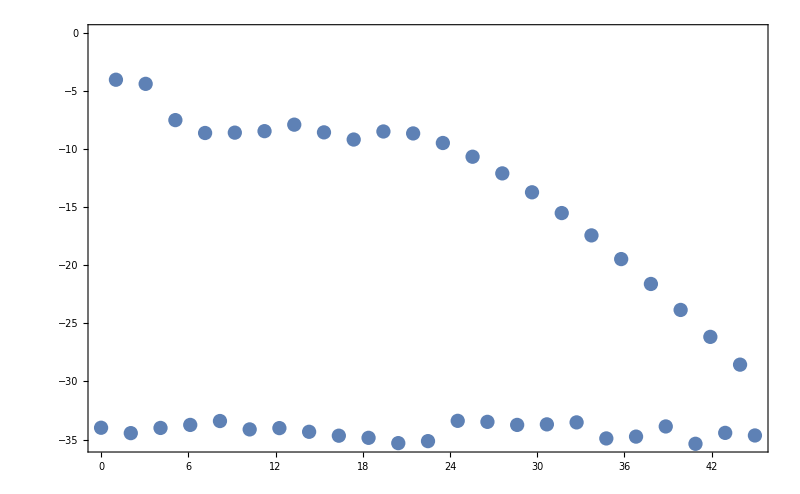

```mathematica
spectrumPlotter[getSpectrum[Most[simpleDipole]],Joined->False]
```

Note here the use of Most on the dipole when a monochromatic field is indicated. This ensures that the signal is actually periodic (i.e. it eliminates repetition between the initial and final points, which are separated by exactly one period). If this is not done, the spectrum is much noisier:

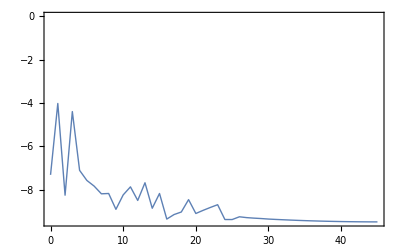

```mathematica
spectrumPlotter[getSpectrum[simpleDipole],ImageSize->400]
```

The default options are built for a periodic pulse for which simple functions of the vector potential can be integrated analytically, and for which only a single period of integration is necessary. More periods can be specified using the TotalCycles option. Similarly, the PointsPerCycle option controls the number of points per period.

```mathematica
AbsoluteTiming[
biggerDipole=makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],FieldParameters->{F->0.05,ω->0.057},TotalCycles->4,PointsPerCycle->150];
]
```

{22.4014,Null}

To get a correct spectrum plot, give these settings to the spectrum plotter.

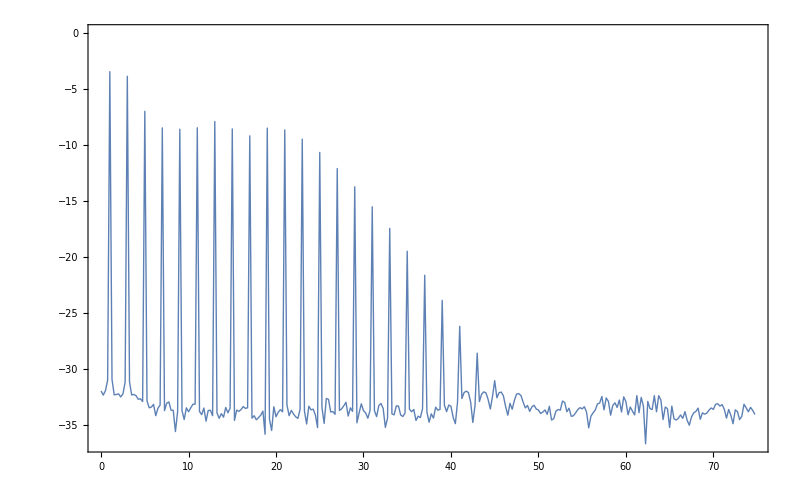

```mathematica
spectrumPlotter[getSpectrum[Most[biggerDipole]],TotalCycles->4,PointsPerCycle->150]
```

To specify the ionization potential of the target, use the option IonizationPotential:

```mathematica
?IonizationPotential
```

IonizationPotential is an option for makeDipole list which specifies the ionization potential I_p of the target.

To see the available options for this function (and others), use

```mathematica
Options[makeDipoleList]
```

{PointsPerCycle→90,TotalCycles→1,CarrierFrequency→0.057,VectorPotential→Automatic,FieldParameters→{},VectorPotentialGradient→None,Preintegrals→Analytic,ReportingFunction→Identity,Gate→SineSquaredGate[1/2],nGate→3/2,ϵCorrection→0.1,IonizationPotential→0.5,PointNumberCorrection→0,Verbose→0}

All options have suitable information messages.

```mathematica
?VectorPotential
```

VectorPotential is an option for makeDipole list which specifies the field's vector potential. Usage should be VectorPotential→A, where A[t]//.pars must yield a list of numbers for numeric t and parameters indicated by FieldParameters→pars.

### Using numerical integration

To simulate a pulse with an envelope, it can be convenient to perform the preintegrals numerically, using the option Preintegrals→”Numeric”. These cases are generally slower but mainly because they require many more periods of integration.

```mathematica
AbsoluteTiming[
numericallyIntegratedDipole=makeDipoleList[VectorPotential->Function[t,{F/ω envelope[t]Sin[ω t],0,0}],FieldParameters->{ω->0.057,F->0.055,envelope->cosPowerFlatTop[0.057,8,16]},TotalCycles->8,Preintegrals->"Numeric"];
]
```

{16.0119,Null}

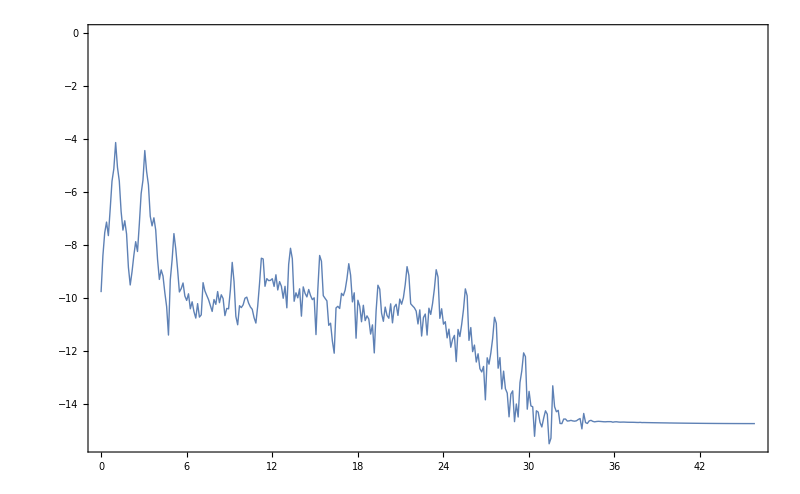

```mathematica
spectrumPlotter[getSpectrum[numericallyIntegratedDipole]]
```

When using flat top pulses, and other waveforms that depend on Piecewise functions, it is possible that the function will return errors caused by an Indeterminate derivative being evaluated at the corners of the envelope.

```mathematica
AbsoluteTiming[
flatTopPulseDipole=makeDipoleList[VectorPotential->Function[t,{F/ω envelope[t]Sin[ω t],0,0}],FieldParameters->{ω->0.057,F->0.055,envelope->flatTopEnvelope[0.057,8,2]},TotalCycles->8,Preintegrals->"Numeric"];
]
```

{17.7842,Null}

In these cases, use a numeric test to diagnose what’s happened

```mathematica
Tally[flatTopPulseDipole/._?NumberQ->✓]
```

{{{✓,✓,✓},721}}

and if the function is returning non-numeric values, it can help to fiddle with the PointNumberCorrection option.

```mathematica
?PointNumberCorrection
```

PointNumberCorrection is an option for makeDipole list which specifies an extra number of points to be integrated over, which is useful to prevent Indeterminate errors when a Piecewise envelope is being differentiated at the boundaries.

### Parallelized environments

The numerical integration can be parallelized over via the use of ParallelTable and similar commands. Care must be taken to ensure that all parallel kernels have the package definitions available (using DistributeDefinitions, ParallelNeeds, or similar constructs). If a variable or function is used to store the results, this must be synchronized using SetSharedFunction or SetSharedVariable, as usual.

```mathematica
DistributeDefinitions["RBSFA`"];
SetSharedFunction[wavelengthScanDipole];

ParallelTable[
Print[AbsoluteTiming[
wavelengthScanDipole[λ]=makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],FieldParameters->{F->0.05,ω->45.6/λ},CarrierFrequency->45.6/λ,PointsPerCycle->400];
]]
,{λ,800,1600,100}]
```

{65.3966,Null}

{67.5219,Null}

{67.9824,Null}

{68.8184,Null}

{70.7804,Null}

{70.9155,Null}

{71.6026,Null}

{43.4543,Null}

{41.8719,Null}

{Null,Null,Null,Null,Null,Null,Null,Null,Null}

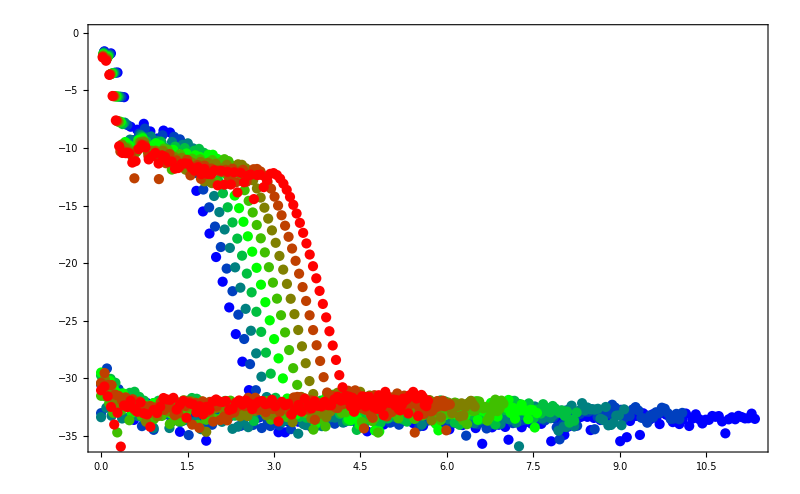

```mathematica
Show[Table[
spectrumPlotter[getSpectrum[Most[wavelengthScanDipole[λ]]],PlotStyle->Blend[{Blue,Green,Red},λ/800-1],CarrierFrequency->45.6/λ,Joined->False,FrequencyAxis->"Frequency",PointsPerCycle->400]
,{λ,800,1600,100}]]
```

### Writing output to file

For very large calculations (many integration points per cycle, in particular), the limiting factor is available memory. In these situations, it can help to write the data directly to a file on disk. This is slower (by a factor of about 2) but it has a roughly constant RAM footprint, so it enables calculations of a bigger size than would be possible otherwise. (Of course, this can also be done from non-parallelized calls!) This is done via the ReportingFunction option:

```mathematica
?ReportingFunction
```

ReportingFunction is an option for makeDipole list which specifies a function used to report the results, either internally (by the default, Identity) or to an external file.

In essence, the integration loop consists of a Table construct, which goes over the time t at which the integral is performed, and an inner integration construct. Setting an option ReportingFunction→f interposes the function  f  between these two steps, as

        Table[  f[  integrator[t]   ]    , {t, tInitial, tFinal}]

The default is f=Identity, which returns its input untouched, but it can also be replaced by a Write construct that can shunt its input to the hard disk without telling the kernel what it is, so it is not kept in memory.

```mathematica
Quit
```

```mathematica
DistributeDefinitions["RBSFA`"];
directory=NotebookDirectory[];
filename[F_]:=FileNameJoin[{directory,"Field scan data at F="<>ToString[F]<>".txt"}];

ParallelTable[
Print[AbsoluteTiming[
makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],FieldParameters->{ω->0.057},CarrierFrequency->0.057,PointsPerCycle->400,
ReportingFunction->Function[Write[filename[F],#]]
];
]]
,{F,0.05,0.2,0.025}]
```

{66.2765,Null}

{68.2327,Null}

{68.4573,Null}

{69.0505,Null}

{69.6457,Null}

{69.8211,Null}

{70.4778,Null}

{Null,Null,Null,Null,Null,Null,Null}

The data in the files can then be pulled in quite simply using e.g.

```mathematica
Do[  intensityScanDipole[F]=ReadList[filename[F]],{F,0.05,0.2,0.025}]
```

This tends to litter the directories by creating lots of files for different parameters, so it is usually cleaner to Save them into a single file, e.g. using

```mathematica
Save[FileNameJoin[{NotebookDirectory[],"Field scan collected data.txt"}],intensityScanDipole]
```

which in turn can then be pulled in using

```mathematica
<<(FileNameJoin[{NotebookDirectory[],"Field scan collected data.txt"}]);
```

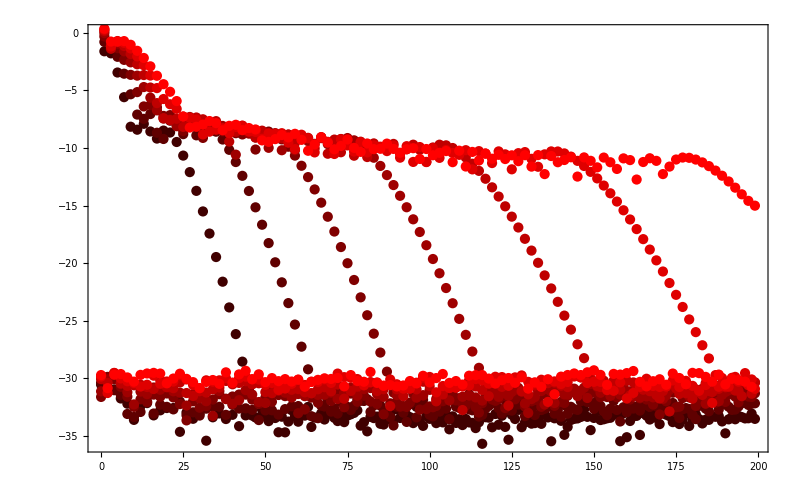

```mathematica
Show[Table[
spectrumPlotter[getSpectrum[Most[intensityScanDipole[F]]],CarrierFrequency->0.057,Joined->False,PointsPerCycle->400,PlotStyle->Blend[{Black,Red},F/0.2]]
,{F,0.05,0.2,0.025}]]
```

As written, though, this has the disadvantage that each subkernel must access the hard drive for every timestep of the computation, which obviously responsible for (at least most of) the slowdown. A middle ground is also possible by choosing an appropriate ReportingFunction: a function which will cache a specific number k of results on RAM, and then write them to file all in one go. This is on the development to do (wish) list, and will hopefully be implemented soon - if time allows.

### Nondipole contributions

Nondipole contributions can be specified by setting a nonzero vector potential gradient:

```mathematica
?VectorPotentialGradient
```

"VectorPotentialGradient is an option for makeDipole list which specifies the gradient of the field's vector potential. Usage should be VectorPotentialGradient→GA, where GA[t]//.pars must yield a square matrix of the same dimension as the vector potential for numeric t and parameters indicated by FieldParameters→pars. The indices must be such that GA[t]⟦i,j⟧ returns ∂_i A_j[t]."

If, for example, the travelling-wave form of the vector potential is of the form A(r,t)=F/ω x̂ cos(k z-ω t), then at the origin the vector potential is A(0,t)=F/ω x̂ cos(ω t) and it has a single nonzero entry in its gradient matrix ∇A, i.e. ∂_z A_x=-(k F)/ωsin(ωt). This is entered into the VectorPotentialGradient option as

```mathematica
nonDipoleContributions=makeDipoleList[
VectorPotential->Function[t,{F/ω Cos[ω t],0,0}],
VectorPotentialGradient->Function[t,{{0,0,0},{0,0,0},{-(k F)/ω Sin[ω t],0,0}}],
FieldParameters->{F->0.05,ω->0.057,k->ω/c,c->137}
];
```

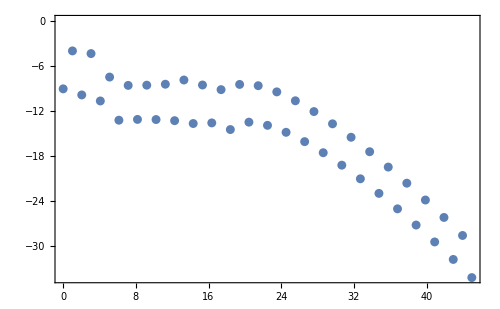

```mathematica
spectrumPlotter[getSpectrum[Most[nonDipoleContributions]],Joined->False,ImageSize->500]
```

At low wavelengths, the first obvious effect is the appearance of even harmonics. This is the expected behaviour, with the harmonics along the laser propagation direction. (Informally, the magnetic pushing on the wavepacket acts on the propagation direction on both halves of each laser period. This off-axis recollision causes the dipole to oscillate in the propagation direction with an even symmetry. More formally, the dynamical symmetries of the problem permit even (but not odd) harmonics along this direction.) This is indeed what is observed:

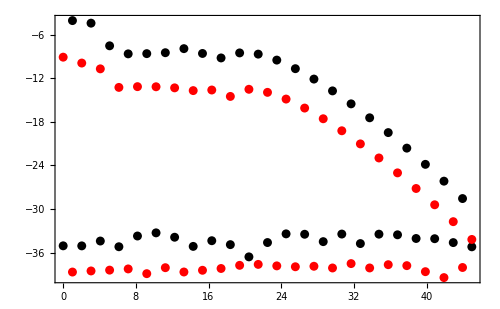

```mathematica
Show[{
spectrumPlotter[getSpectrum[nonDipoleContributions⟦1;;-2,{1,2}⟧],Joined->False,PlotStyle->Black],
spectrumPlotter[getSpectrum[nonDipoleContributions⟦1;;-2,{3}⟧],Joined->False,PlotStyle->Red]
},PlotRange->All,ImageSize->500]
```

### Debugging and benchmarking tools

If something goes funny with your calls, then before you start taking makeDipoleList apart you can try using its Verbose option to diagnose the internal functions it is using. In particular:

Setting Verbose→1 makes makeDipoleList print the Information of the key internal functions it is using, before it goes on to the integration loop.

```mathematica
makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],FieldParameters->{F->0.05,ω->0.057},Verbose->1]⟦1;;10⟧
```

RBSFA`Private`ps

RBSFA`Private`ps[RBSFA`Private`t_?RBSFA`Private`gridPointQ,RBSFA`Private`tt_?RBSFA`Private`gridPointQ]:=RBSFA`Private`ps[RBSFA`Private`t,RBSFA`Private`tt]=-1/(RBSFA`Private`t-RBSFA`Private`tt-ⅈ RBSFA`Private`ϵ)Inverse[IdentityMatrix[Length[RBSFA`Private`A[RBSFA`Private`tInit]]]-(RBSFA`Private`GAIntInt[RBSFA`Private`t,RBSFA`Private`tt]+Transpose[RBSFA`Private`GAIntInt[RBSFA`Private`t,RBSFA`Private`tt]])/(RBSFA`Private`t-RBSFA`Private`tt-ⅈ RBSFA`Private`ϵ)].(RBSFA`Private`AInt[RBSFA`Private`t,RBSFA`Private`tt]-RBSFA`Private`bigPScorrectionInt[RBSFA`Private`t,RBSFA`Private`tt])

RBSFA`Private`pi

RBSFA`Private`pi[RBSFA`Private`p_,RBSFA`Private`t_]:=RBSFA`Private`p+RBSFA`Private`A[RBSFA`Private`t]-RBSFA`Private`GAInt[RBSFA`Private`t].RBSFA`Private`p-RBSFA`Private`GAdotAInt[RBSFA`Private`t]

RBSFA`Private`S

RBSFA`Private`S[RBSFA`Private`t_?RBSFA`Private`gridPointQ,RBSFA`Private`tt_?RBSFA`Private`gridPointQ]:=1/2 (Norm[RBSFA`Private`ps[RBSFA`Private`t,RBSFA`Private`tt]]^2+(RBSFA`Private`κ)^2) (RBSFA`Private`t-RBSFA`Private`tt)+RBSFA`Private`ps[RBSFA`Private`t,RBSFA`Private`tt].RBSFA`Private`AInt[RBSFA`Private`t,RBSFA`Private`tt]+1/2 RBSFA`Private`A2Int[RBSFA`Private`t,RBSFA`Private`tt]-(RBSFA`Private`ps[RBSFA`Private`t,RBSFA`Private`tt].RBSFA`Private`GAIntInt[RBSFA`Private`t,RBSFA`Private`tt].RBSFA`Private`ps[RBSFA`Private`t,RBSFA`Private`tt]+RBSFA`Private`ps[RBSFA`Private`t,RBSFA`Private`tt].RBSFA`Private`bigPScorrectionInt[RBSFA`Private`t,RBSFA`Private`tt]+RBSFA`Private`AdotGAdotAInt[RBSFA`Private`t,RBSFA`Private`tt])

RBSFA`Private`AInt

RBSFA`Private`AInt[RBSFA`Private`t$_]={-15.3894 Cos[0.057 RBSFA`Private`t$],0,0}
 
RBSFA`Private`AInt[RBSFA`Private`t$_,RBSFA`Private`tt$_]={15.3894 Cos[0.057 RBSFA`Private`tt$]-15.3894 Cos[0.057 RBSFA`Private`t$],0,0}

(abridged.)

{{-0.0198736+0.00113629 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.0166186-1.44349 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.0132498-5.34015 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.00957477-10.5721 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.00563402-15.8027 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.00185819-19.9418 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.00123386-22.4066 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.00353492-23.1295 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.0053967-22.4 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.00707192-20.6646 ⅈ,0.+0. ⅈ,0.+0. ⅈ}}

Setting Verbose→2 makes makeDipoleList output its key internal functions and shut down before the integration takes place. Its results can be caught as follows:

```mathematica
{ps[t_,tt_],pi[p_,t_],S[t_,tt_],AInt[t_],AInt[t_,tt_],A2Int[t_],A2Int[t_,tt_],GAInt[t_],GAInt[t_,tt_],GAdotAInt[t_],GAdotAInt[t_,tt_],AdotGAInt[t_],AdotGAInt[t_,tt_],GAIntInt[t_],GAIntInt[t_,tt_],bigPScorrectionInt[t_],bigPScorrectionInt[t_,tt_],AdotGAdotAInt[t_],AdotGAdotAInt[t_,tt_],integrand[t_,τ_]
}=makeDipoleList[VectorPotential->Function[t,{F/ω Sin[ω t],0,0}],FieldParameters->{F->0.05,ω->0.057},Verbose->2];
```

This then enables examination of e.g. the action:

```mathematica
Block[{ω=0.057},
Plot3D[
Im[S[t,tt]]
,{t,0,3(2π)/ω},{tt,0,3(2π)/ω}
,PlotRange->Full,ImageSize->600,PlotTheme->"Classic",PlotPoints->100
]
]
```

-Graphics3D-

See the implementation notes in the code for makeDipoleList for further definitions of what each term entails.

### Bicircular fields

As a slightly less trivial example, consider a bicircular field: two counter-rotating, circularly polarized fields of different frequencies. The ‘standard’ case - as first demonstrated experimentally - has one field as the second harmonic of the fundamental, with both at equal intensities. The resultant harmonics appear at all integer orders except those divisible by three, with the 3n+1 harmonics polarized as the fundamental, and the 3n-1 harmonics polarized as the second-harmonic driver.

```mathematica
bicircularA[t_]:=(F1/ω1{ Cos[t ω1] Sin[α],- Cos[α] Sin[t ω1]}+F2/ω2{Cos[β]Cos[ω2 t],Sin[β]Sin[ω2 t]})
bicircularParameters={F1->0.075,F2->0.075,α->45°,β->45°,ω1->45.6/800,ω2->45.6/400};
AbsoluteTiming[bicircularTest=makeDipoleList[VectorPotential->bicircularA,FieldParameters->bicircularParameters,TotalCycles->4];]
```

{8.45739,Null}

The function biColorSpectrum takes the spectrum and plots it, separating the two circular polarizations into different colours.

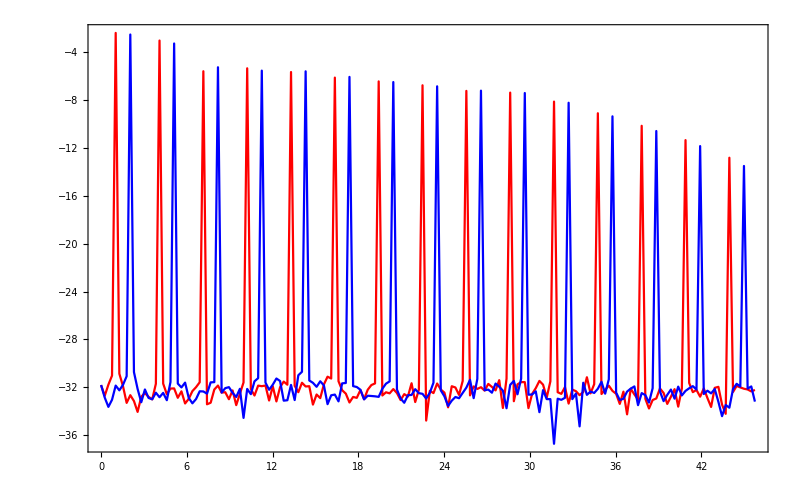

```mathematica
biColorSpectrum[Most[bicircularTest]]
```

### Bicircular fields with a sine-squared envelope

To benchmark the original calculations, we compared them with the output of full MCTDH calculations. Here we used a sin^2 envelope as the TDSE numerics require a finite pulse; the calculations take correspondingly longer but they are still very manageable (two/three minutes per calculation for a fifteen-cycle pulse, resolving up to ~70 harmonics). One distinctive feature is that the harmonics near the cutoff are broader, because less cycles contribute to those energies.

```mathematica
bicircularEnvelopeA[t_]:=cosPowerFlatTop[ω1,TotalCycles,2][t](F1/ω1{ Cos[t ω1] Sin[α],- Cos[α] Sin[t ω1]}+F2/ω2{Cos[β]Cos[ω2 t],Sin[β]Sin[ω2 t]});
bicircularParameters={F1->0.075,F2->0.075,α->45°,β->45°,ω1->45.6/800,ω2->45.6/400};
```

If (as in this case) the field depends on a number-of-cycles parameter, care must be taken that it matches the num option of the main call.

```mathematica
AbsoluteTiming[
bicircularEnvelopeDipole=makeDipoleList[VectorPotential->bicircularEnvelopeA,FieldParameters->Join[bicircularParameters,{TotalCycles->15}],PointsPerCycle->150,TotalCycles->15];
]
```

{141.302,Null}

Plotting the spectrum, and a zoom at the plateau:

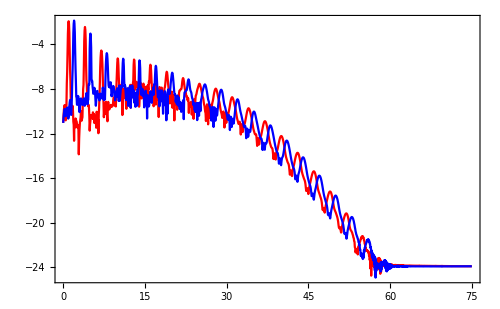

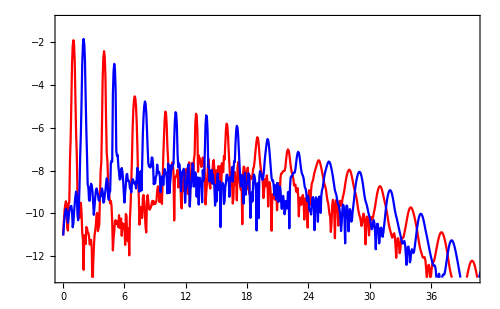

```mathematica
biColorSpectrum[bicircularEnvelopeDipole,PointsPerCycle->150,TotalCycles->15,ImageSize->500]
biColorSpectrum[bicircularEnvelopeDipole,PointsPerCycle->150,TotalCycles->15,ImageSize->500,PlotRange->{{0,40},{-13,-1}}]
```

The comparable MCTDH spectrum, for identical conditions, looks like this:

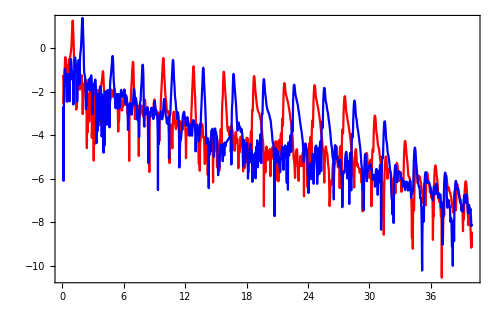

### Original RB-SFA: ‘rotating’ bicircular fields

#### Calculation

Here the fundamental laser driver has been set at an elliptical polarization (as in the original experiment, A. Fleischer et al., Nature Photon. 8, 543 (2014)), which helps investigate the spin-angular-momentum conservation properties of HHG. In the model proposed in the original paper (Phys. Rev. A 90, 043829 (2014)), the photon model is validated by splitting the elliptical field itself into two circular components, which can then be tuned independently:

```mathematica
rotatingBicircularA[t_]:=envelope[t](F2/ω2{Cos[β]Cos[ω2 t-ϕ1],Sin[β]Sin[ω2 t-ϕ1]}+F1/(√2)(1/ω1 Cos[α-π/4]{Cos[ω1 t+ϕ1],-Sin[ω1 t+ϕ1]}+1/((1+δ)ω1)Sin[α-π/4]{Cos[(1+δ)ω1 t-ϕ1+ϕ2],+Sin[(1+δ)ω1 t -ϕ1+ϕ2]}));
```

```mathematica
DistributeDefinitions["RBSFA`"];
directory=FileNameJoin[{NotebookDirectory[],"Temp Data"}];
filename[δ_]:=FileNameJoin[{directory,"data 25.09 detuning scan at δ="<>ToString[δ]<>".txt"}];
Length[δRange=Range[0,0.25,0.001]]
```

251

To test the validity of the photon model, we ran a scan over the detuning δ, using the calculation below.

```mathematica
DateString[]
Print["Total = ",Length[δRange]," points at ~230s/point will be done at approximately ",DateString[AbsoluteTime[]+Length[δRange]*230./7],"."]
ParallelTable[
Print[AbsoluteTiming[
makeDipoleList[
VectorPotential->rotatingBicircularA,
FieldParameters->{α->35 °,β->45 °,F1->0.075,F2->0.075,ω1->0.057,ω2->1.95×0.057,ϕ1->0,ϕ2->0,envelope->flatTopEnvelope[ω1,26,3]},
CarrierFrequency->0.057,TotalCycles->26,PointsPerCycle->115,nGate->1.8,PointNumberCorrection->1,Preintegrals->"Numeric",
ReportingFunction->Function[Write[filename[δ],#]]
];]];
Print[DateString[]];
,{δ,δRange}];
DateString[]
NotebookSave[]
```

Total time 2h 32min. (Desktop machine with 8-thread, 4-core Intel i7-3770 CPU at 3.40GHz, 16GB RAB, running 7 Mathematica kernels in parallel.)
Expand this cell to see the calculation log.

Fri 25 Sep 2015 23:54:59

Total = 251 points at ~230s/point will be done at approximately Sat 26 Sep 2015 02:12:26.

{243.449,Null}

Fri 25 Sep 2015 23:59:03

{254.907,Null}

Fri 25 Sep 2015 23:59:14

{256.794,Null}

Fri 25 Sep 2015 23:59:16

{257.342,Null}

Fri 25 Sep 2015 23:59:17

{257.439,Null}

{257.496,Null}

Fri 25 Sep 2015 23:59:17

Fri 25 Sep 2015 23:59:17

{258.157,Null}

Fri 25 Sep 2015 23:59:18

{256.621,Null}

Sat 26 Sep 2015 00:03:20

{257.176,Null}

Sat 26 Sep 2015 00:03:32

{256.457,Null}

Sat 26 Sep 2015 00:03:33

{257.858,Null}

Sat 26 Sep 2015 00:03:35

{257.249,Null}

Sat 26 Sep 2015 00:03:35

{258.549,Null}

Sat 26 Sep 2015 00:03:35

{262.01,Null}

Sat 26 Sep 2015 00:03:39

{257.52,Null}

Sat 26 Sep 2015 00:07:37

{255.313,Null}

Sat 26 Sep 2015 00:07:47

{257.303,Null}

Sat 26 Sep 2015 00:07:50

{256.504,Null}

Sat 26 Sep 2015 00:07:51

{256.676,Null}

Sat 26 Sep 2015 00:07:51

{257.886,Null}

Sat 26 Sep 2015 00:07:53

{258.438,Null}

Sat 26 Sep 2015 00:07:57

{259.005,Null}

Sat 26 Sep 2015 00:11:56

{255.526,Null}

Sat 26 Sep 2015 00:12:02

{255.989,Null}

Sat 26 Sep 2015 00:12:07

{257.398,Null}

Sat 26 Sep 2015 00:12:07

{258.373,Null}

Sat 26 Sep 2015 00:12:10

{259.41,Null}

Sat 26 Sep 2015 00:12:13

{257.386,Null}

Sat 26 Sep 2015 00:12:15

{253.567,Null}

Sat 26 Sep 2015 00:16:10

{256.773,Null}

Sat 26 Sep 2015 00:16:19

{256.932,Null}

Sat 26 Sep 2015 00:16:24

{258.164,Null}

Sat 26 Sep 2015 00:16:26

{255.857,Null}

Sat 26 Sep 2015 00:16:26

{256.819,Null}

Sat 26 Sep 2015 00:16:32

{260.329,Null}

Sat 26 Sep 2015 00:16:33

{257.695,Null}

Sat 26 Sep 2015 00:20:27

{254.694,Null}

Sat 26 Sep 2015 00:20:34

{257.262,Null}

Sat 26 Sep 2015 00:20:42

{256.648,Null}

Sat 26 Sep 2015 00:20:42

{258.688,Null}

Sat 26 Sep 2015 00:20:44

{257.148,Null}

Sat 26 Sep 2015 00:20:50

{260.138,Null}

Sat 26 Sep 2015 00:20:52

{255.577,Null}

Sat 26 Sep 2015 00:24:49

{262.37,Null}

Sat 26 Sep 2015 00:24:50

{255.263,Null}

Sat 26 Sep 2015 00:24:57

{256.929,Null}

Sat 26 Sep 2015 00:24:59

{260.329,Null}

Sat 26 Sep 2015 00:25:05

{254.807,Null}

Sat 26 Sep 2015 00:25:07

{257.474,Null}

Sat 26 Sep 2015 00:25:08

{254.524,Null}

Sat 26 Sep 2015 00:29:04

{257.08,Null}

Sat 26 Sep 2015 00:29:07

{256.669,Null}

Sat 26 Sep 2015 00:29:15

{258.81,Null}

Sat 26 Sep 2015 00:29:16

{253.721,Null}

Sat 26 Sep 2015 00:29:18

{254.744,Null}

Sat 26 Sep 2015 00:29:21

{254.037,Null}

Sat 26 Sep 2015 00:29:22

{254.339,Null}

Sat 26 Sep 2015 00:33:18

{255.706,Null}

Sat 26 Sep 2015 00:33:22

{249.275,Null}

Sat 26 Sep 2015 00:33:26

{252.394,Null}

Sat 26 Sep 2015 00:33:28

{253.764,Null}

Sat 26 Sep 2015 00:33:32

{252.286,Null}

Sat 26 Sep 2015 00:33:34

{253.999,Null}

Sat 26 Sep 2015 00:33:35

{251.872,Null}

Sat 26 Sep 2015 00:37:30

{251.841,Null}

Sat 26 Sep 2015 00:37:34

{250.071,Null}

Sat 26 Sep 2015 00:37:36

{252.216,Null}

Sat 26 Sep 2015 00:37:40

{250.313,Null}

Sat 26 Sep 2015 00:37:44

{252.188,Null}

Sat 26 Sep 2015 00:37:45

{253.911,Null}

Sat 26 Sep 2015 00:37:49

{252.658,Null}

Sat 26 Sep 2015 00:41:43

{249.291,Null}

Sat 26 Sep 2015 00:41:45

{251.75,Null}

Sat 26 Sep 2015 00:41:46

{253.848,Null}

Sat 26 Sep 2015 00:41:54

{250.81,Null}

Sat 26 Sep 2015 00:41:55

{253.741,Null}

Sat 26 Sep 2015 00:41:58

{252.087,Null}

Sat 26 Sep 2015 00:42:02

{251.429,Null}

Sat 26 Sep 2015 00:45:54

{250.527,Null}

Sat 26 Sep 2015 00:45:56

{252.765,Null}

Sat 26 Sep 2015 00:45:59

{251.482,Null}

Sat 26 Sep 2015 00:46:07

{254.13,Null}

Sat 26 Sep 2015 00:46:08

{250.409,Null}

Sat 26 Sep 2015 00:46:09

{252.258,Null}

Sat 26 Sep 2015 00:46:14

{249.626,Null}

Sat 26 Sep 2015 00:50:05

{252.681,Null}

Sat 26 Sep 2015 00:50:07

{252.079,Null}

Sat 26 Sep 2015 00:50:11

{250.28,Null}

Sat 26 Sep 2015 00:50:18

{252.295,Null}

Sat 26 Sep 2015 00:50:19

{251.678,Null}

Sat 26 Sep 2015 00:50:20

{253.414,Null}

Sat 26 Sep 2015 00:50:27

{248.014,Null}

Sat 26 Sep 2015 00:54:13

{251.171,Null}

Sat 26 Sep 2015 00:54:18

{252.743,Null}

Sat 26 Sep 2015 00:54:24

{248.42,Null}

Sat 26 Sep 2015 00:54:29

{252.651,Null}

Sat 26 Sep 2015 00:54:32

{254.747,Null}

Sat 26 Sep 2015 00:54:33

{256.036,Null}

Sat 26 Sep 2015 00:54:43

{248.918,Null}

Sat 26 Sep 2015 00:58:22

{250.23,Null}

Sat 26 Sep 2015 00:58:28

{253.976,Null}

Sat 26 Sep 2015 00:58:38

{252.674,Null}

Sat 26 Sep 2015 00:58:41

{251.011,Null}

Sat 26 Sep 2015 00:58:44

{253.237,Null}

Sat 26 Sep 2015 00:58:45

{254.193,Null}

Sat 26 Sep 2015 00:58:57

{248.801,Null}

Sat 26 Sep 2015 01:02:31

{249.892,Null}

Sat 26 Sep 2015 01:02:38

{253.766,Null}

Sat 26 Sep 2015 01:02:51

{250.716,Null}

Sat 26 Sep 2015 01:02:52

{252.986,Null}

Sat 26 Sep 2015 01:02:57

{253.294,Null}

Sat 26 Sep 2015 01:02:58

{254.339,Null}

Sat 26 Sep 2015 01:03:12

{249.249,Null}

Sat 26 Sep 2015 01:06:40

{254.651,Null}

Sat 26 Sep 2015 01:06:53

{251.019,Null}

Sat 26 Sep 2015 01:07:03

{251.432,Null}

Sat 26 Sep 2015 01:07:04

{252.609,Null}

Sat 26 Sep 2015 01:07:10

{255.379,Null}

Sat 26 Sep 2015 01:07:14

{252.54,Null}

Sat 26 Sep 2015 01:07:24

{250.084,Null}

Sat 26 Sep 2015 01:10:50

{253.436,Null}

Sat 26 Sep 2015 01:11:06

{251.095,Null}

Sat 26 Sep 2015 01:11:15

{253.333,Null}

Sat 26 Sep 2015 01:11:16

{250.522,Null}

Sat 26 Sep 2015 01:11:20

{253.204,Null}

Sat 26 Sep 2015 01:11:27

{252.571,Null}

Sat 26 Sep 2015 01:11:37

{249.371,Null}

Sat 26 Sep 2015 01:15:00

{253.51,Null}

Sat 26 Sep 2015 01:15:20

{254.336,Null}

Sat 26 Sep 2015 01:15:29

{253.652,Null}

Sat 26 Sep 2015 01:15:30

{256.302,Null}

Sat 26 Sep 2015 01:15:37

{252.93,Null}

Sat 26 Sep 2015 01:15:40

{253.634,Null}

Sat 26 Sep 2015 01:15:51

{251.119,Null}

Sat 26 Sep 2015 01:19:11

{252.183,Null}

Sat 26 Sep 2015 01:19:32

{251.577,Null}

Sat 26 Sep 2015 01:19:41

{254.152,Null}

Sat 26 Sep 2015 01:19:43

{252.267,Null}

Sat 26 Sep 2015 01:19:49

{254.025,Null}

Sat 26 Sep 2015 01:19:54

{251.914,Null}

Sat 26 Sep 2015 01:20:03

{252.455,Null}

Sat 26 Sep 2015 01:23:23

{252.665,Null}

Sat 26 Sep 2015 01:23:45

{252.913,Null}

Sat 26 Sep 2015 01:23:54

{251.737,Null}

Sat 26 Sep 2015 01:23:55

{252.655,Null}

Sat 26 Sep 2015 01:24:02

{254.643,Null}

Sat 26 Sep 2015 01:24:09

{254.561,Null}

Sat 26 Sep 2015 01:24:17

{251.304,Null}

Sat 26 Sep 2015 01:27:35

{252.381,Null}

Sat 26 Sep 2015 01:27:57

{250.912,Null}

Sat 26 Sep 2015 01:28:06

{253.389,Null}

Sat 26 Sep 2015 01:28:08

{254.54,Null}

Sat 26 Sep 2015 01:28:16

{252.447,Null}

Sat 26 Sep 2015 01:28:21

{250.941,Null}

Sat 26 Sep 2015 01:28:28

{251.042,Null}

Sat 26 Sep 2015 01:31:46

{253.258,Null}

Sat 26 Sep 2015 01:32:11

{253.693,Null}

Sat 26 Sep 2015 01:32:20

{255.796,Null}

Sat 26 Sep 2015 01:32:23

{252.292,Null}

Sat 26 Sep 2015 01:32:28

{251.498,Null}

Sat 26 Sep 2015 01:32:33

{253.874,Null}

Sat 26 Sep 2015 01:32:42

{250.817,Null}

Sat 26 Sep 2015 01:35:57

{254.017,Null}

Sat 26 Sep 2015 01:36:25

{250.89,Null}

Sat 26 Sep 2015 01:36:31

{254.441,Null}

Sat 26 Sep 2015 01:36:38

{251.566,Null}

Sat 26 Sep 2015 01:36:40

{254.02,Null}

Sat 26 Sep 2015 01:36:47

{253.733,Null}

Sat 26 Sep 2015 01:36:56

{248.917,Null}

Sat 26 Sep 2015 01:40:06

{252.298,Null}

Sat 26 Sep 2015 01:40:37

{253.614,Null}

Sat 26 Sep 2015 01:40:44

{252.666,Null}

Sat 26 Sep 2015 01:40:50

{255.123,Null}

Sat 26 Sep 2015 01:40:55

{252.493,Null}

Sat 26 Sep 2015 01:40:59

{255.39,Null}

Sat 26 Sep 2015 01:41:11

{248.751,Null}

Sat 26 Sep 2015 01:44:14

{253.427,Null}

Sat 26 Sep 2015 01:44:50

{250.359,Null}

Sat 26 Sep 2015 01:44:55

{255.603,Null}

Sat 26 Sep 2015 01:45:06

{252.843,Null}

Sat 26 Sep 2015 01:45:08

{254.434,Null}

Sat 26 Sep 2015 01:45:14

{253.936,Null}

Sat 26 Sep 2015 01:45:25

{249.489,Null}

Sat 26 Sep 2015 01:48:24

{254.609,Null}

Sat 26 Sep 2015 01:49:05

{252.49,Null}

Sat 26 Sep 2015 01:49:07

{252.409,Null}

Sat 26 Sep 2015 01:49:18

{254.696,Null}

Sat 26 Sep 2015 01:49:23

{253.177,Null}

Sat 26 Sep 2015 01:49:27

{255.789,Null}

Sat 26 Sep 2015 01:49:41

{248.62,Null}

Sat 26 Sep 2015 01:52:33

{254.66,Null}

Sat 26 Sep 2015 01:53:20

{253.74,Null}

Sat 26 Sep 2015 01:53:21

{253.78,Null}

Sat 26 Sep 2015 01:53:32

{251.811,Null}

Sat 26 Sep 2015 01:53:35

{254.042,Null}

Sat 26 Sep 2015 01:53:41

{253.371,Null}

Sat 26 Sep 2015 01:53:54

{249.143,Null}

Sat 26 Sep 2015 01:56:42

{254.544,Null}

Sat 26 Sep 2015 01:57:35

{255.728,Null}

Sat 26 Sep 2015 01:57:36

{253.229,Null}

Sat 26 Sep 2015 01:57:46

{257.017,Null}

Sat 26 Sep 2015 01:57:52

{252.004,Null}

Sat 26 Sep 2015 01:57:53

{254.533,Null}

Sat 26 Sep 2015 01:58:09

{252.019,Null}

Sat 26 Sep 2015 02:00:54

{251.881,Null}

Sat 26 Sep 2015 02:01:47

{252.105,Null}

Sat 26 Sep 2015 02:01:48

{251.961,Null}

Sat 26 Sep 2015 02:01:58

{252.435,Null}

Sat 26 Sep 2015 02:02:04

{253.186,Null}

Sat 26 Sep 2015 02:02:06

{254.602,Null}

Sat 26 Sep 2015 02:02:23

{251.084,Null}

Sat 26 Sep 2015 02:05:05

{250.27,Null}

Sat 26 Sep 2015 02:05:58

{252.045,Null}

Sat 26 Sep 2015 02:06:00

{254.221,Null}

Sat 26 Sep 2015 02:06:12

{255.596,Null}

Sat 26 Sep 2015 02:06:20

{253.951,Null}

Sat 26 Sep 2015 02:06:20

{255.577,Null}

Sat 26 Sep 2015 02:06:39

{247.568,Null}

Sat 26 Sep 2015 02:09:12

{252.734,Null}

Sat 26 Sep 2015 02:10:10

{252.616,Null}

Sat 26 Sep 2015 02:10:12

{254.627,Null}

Sat 26 Sep 2015 02:10:27

{252.523,Null}

Sat 26 Sep 2015 02:10:32

{252.796,Null}

Sat 26 Sep 2015 02:10:33

{255.219,Null}

Sat 26 Sep 2015 02:10:54

{251.551,Null}

Sat 26 Sep 2015 02:13:24

{251.664,Null}

Sat 26 Sep 2015 02:14:22

{253.936,Null}

Sat 26 Sep 2015 02:14:26

{252.518,Null}

Sat 26 Sep 2015 02:14:39

{253.397,Null}

Sat 26 Sep 2015 02:14:46

{254.648,Null}

Sat 26 Sep 2015 02:14:48

{253.289,Null}

Sat 26 Sep 2015 02:15:08

{252.79,Null}

Sat 26 Sep 2015 02:17:37

{252.897,Null}

Sat 26 Sep 2015 02:18:35

{256.919,Null}

Sat 26 Sep 2015 02:18:43

{253.88,Null}

Sat 26 Sep 2015 02:18:53

{251.461,Null}

Sat 26 Sep 2015 02:18:57

{255.058,Null}

Sat 26 Sep 2015 02:19:03

{254.171,Null}

Sat 26 Sep 2015 02:19:22

{250.378,Null}

Sat 26 Sep 2015 02:21:47

{255.346,Null}

Sat 26 Sep 2015 02:22:50

{255.272,Null}

Sat 26 Sep 2015 02:22:58

{254.574,Null}

Sat 26 Sep 2015 02:23:08

{253.245,Null}

Sat 26 Sep 2015 02:23:10

{256.747,Null}

Sat 26 Sep 2015 02:23:19

{255.07,Null}

Sat 26 Sep 2015 02:23:37

{241.296,Null}

Sat 26 Sep 2015 02:25:48

{237.181,Null}

Sat 26 Sep 2015 02:26:47

{235.884,Null}

Sat 26 Sep 2015 02:26:54

{230.584,Null}

Sat 26 Sep 2015 02:26:58

{228.565,Null}

Sat 26 Sep 2015 02:26:59

{226.844,Null}

Sat 26 Sep 2015 02:27:06

Sat 26 Sep 2015 02:27:06

The results can be pulled in from the files using this:

```mathematica
Do[detunedDipole[δ]=ReadList[filename[δ]],{δ,δRange}]
```

Or saved into a single location using this:

```mathematica
Save[FileNameJoin[{NotebookDirectory[],"Detuning scan collected data.txt"}],detunedDipole]
```

```mathematica
DumpSave[FileNameJoin[{NotebookDirectory[],"Detuning scan collected data.mx"}],detunedDipole];
```

and pulled in from the single location using this:

```mathematica
<<(FileNameJoin[{NotebookDirectory[],"Detuning scan collected data.txt"}]);
```

A sample spectrum looks like this:

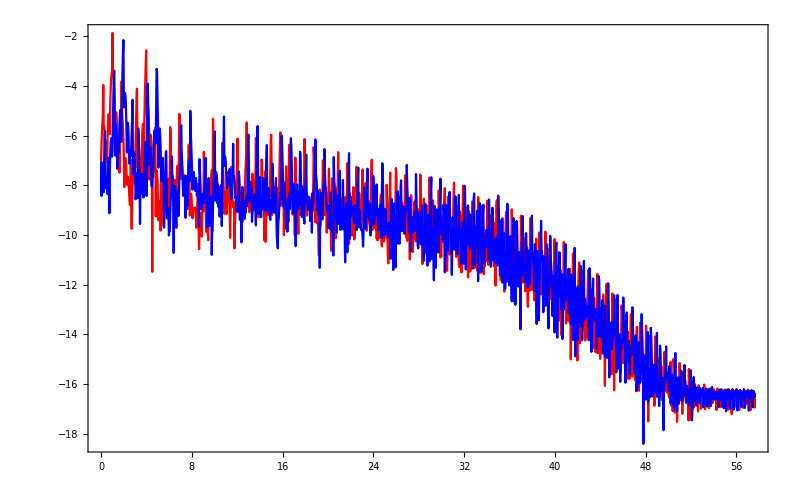

```mathematica
biColorSpectrum[detunedDipole[0.001RandomInteger[{0,1000}]],CarrierFrequency->45.6/800,TotalCycles->3,PointsPerCycle->115]
```

#### Plots from the original paper

The plots from the original paper were produced using the code below. For simplicity we pre-define an interpolation function.

```mathematica
conditions:=Sequence[CarrierFrequency->45.6/800,TotalCycles->26,PointsPerCycle->115]
```

```mathematica
Remove[detuningInterpolation]
With[{length=Length[getSpectrum[detunedDipole[0.],Polarization->{1,ⅈ}]]},
AbsoluteTiming[
Table[
detuningInterpolation[ϵ]=Interpolation[
Flatten[Table[
{{
harmonicOrderAxis[TargetLength->length,conditions],
Table[δ,{length}]
}ᵀ,
Log[10,getSpectrum[detunedDipole[δ],Polarization->{1,ϵ ⅈ}]]
}ᵀ
,{δ,δRange}],1]]
,{ϵ,{1,-1}}];
]
]
```

{2.99829,Null}

Some plotting admin:

```mathematica
CMRmap=Function[x,Blend[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},x]];
CMRwithMin[minIn_,minOut_:1./9]:=Function[x,CMRmap[If[x<minIn,minOut/minIn x,minOut+(1-minOut)(x-minIn)/(1-minIn)]]]
min=6. 10^-9;
max=5. 10^-7;
colorfunction=CMRwithMin[min/max];
HOTicks[ϵ_]:=({#,If[ϵ==1,Style[#,Black],""],{0.02,0},{Thickness[0.005],Gray}}&/@Range[12,18,1])~Join~({#,"",{0.01,0},{Thickness[0.004],Gray}}&/@Range[11+1/2,18+1/4,1/4])
downTicks={{0,Style[0,Black],0},{0.25,Style[0.25,Black],0}}~Join~({#,Style[#,Black],{0.015,0},{Thickness[0.005],Gray}}&/@Range[0.05,0.20,0.05])~Join~({#,"",{0.01,0},{Thickness[0.004],Gray}}&/@Range[0.01,0.24,0.01]);
upTicks=({#,"",{0.015,0},{Thickness[0.005],Gray}}&/@Range[0.05,0.20,0.05])~Join~({#,"",{0.01,0},{Thickness[0.004],Gray}}&/@Range[0.01,0.24,0.01]);
```

The plot itself:

```mathematica
Row[Table[
splittingsScan[ϵ]=RegionPlot[
True
,{δ,0,0.25},{HO,11.25,18.5}
,AspectRatio->1.2
,PlotRangePadding->None
,ImagePadding->1{{35+15ϵ,20},{70,6}}
,ImageSize->{Automatic,550}
,PlotPoints->600
,FrameStyle->Automatic
,FrameLabel->{Style["ω'/ω-1",Black,12],If[ϵ==1,Style["Harmonic Order",Black,16],""]}
,ColorFunctionScaling->False
,FrameTicks->{{HOTicks[1],HOTicks[-1]},{downTicks,upTicks}}
,ColorFunction->Function[{δ,HO},colorfunction[(10^detuningInterpolation[ϵ][HO,δ])/max]]
,PlotLabel->Style[StringJoin[ϵ/.{1->"Right",-1->"Left"},"-circular harmonics"],Black,16]
]
,{ϵ,{1,-1}}]
]
```

(Removed to keep file size low.)